```mathematica
(*set initial conditions*)
x0=Pi/2;
vx0=-1;

y0=0;
vy0=.5;

(*solve coupled system of odes*)
tf=20;

sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]],x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];

s1= x  /. First@sol;
s2= y /. First@sol;

(*plot trajectories*)
hoop =ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
Animate[Show[hoop,ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{RGBColor[0.394, 0.394, 0.394],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{RGBColor[0.668, 0.668, 0.668],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```

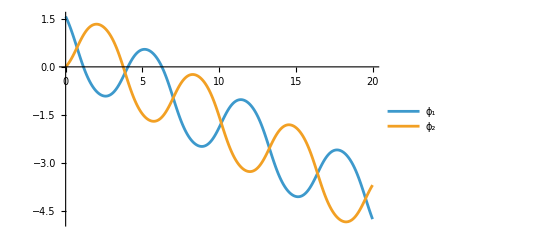

```mathematica
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All]]
```